## Patterns and Rules

Паттерн/pattern x_    
Одиночный паттерн (“пустышка”, “Blank”) - любое число, символ, выражение, что угодно

_		Blank[]				бланк 
__		BlankSequence[] 		непустая последовательность бланков
___		BlankNullSequence[]	последовательность бланков

### Blanks

```mathematica
f[x_]:=x+1 (*x_ -> в качестве аргумента всё что угодно*)
```

```mathematica
{f[4],f[a],f["applied maths"]}
```

{5,1+a,1+applied maths}

#### Сходство по типу (_head) (Pattern matching by type)

```mathematica
MatchQ[3.14,_Real]
```

True

```mathematica
MatchQ[3.14,_Integer]
```

False

```mathematica
Cases[{3,3.14,17,"24",4+5 I},_Integer] (*выбор из списка по образцу*)
```

{3,17}

```mathematica
Cases[{3,3.14,17,"24",4+5 I},_String]
```

{24}

```mathematica
ToCharacterCode[{"24"}]
```

{{50,52}}

```mathematica
Cases[{g[x],f[x],g[h[x]],g[a,0]},_g]
```

{g[x],g[h[x]],g[a,0]}

```mathematica
Cases[{a+b,2+3,"3+4"},_Plus] (* сначала вычислили аргумент функции 2+3, а только потом вызвали Cases*)
```

{a+b}

```mathematica
FullForm[2+3]
```

5

```mathematica
Clear[f]
```

```mathematica
f[x_Integer]:=x+1 (*функция определена только для целых значений аргумента*)
```

```mathematica
{f[-5],f[0],f[5],f[3.14],f[a]}
```

{-4,1,6,f[3.14],f[a]}

#### Сходство по структуре (Structured patterns)

```mathematica
Cases[{{a,b},{},{1,0},{c,d,3}},{p_,q_}] (*список из друх элементов*)
```

{{a,b},{1,0}}

```mathematica
Cases[{{a,b},{},{1,0},{c,d,3}},{_,_}] (* тоже самое*)
```

{{a,b},{1,0}}

```mathematica
Cases[{2,9/3,1/3,x/(y+z)},a_/b_]
```

{x/(y+z)}

```mathematica
{FullForm[1/3],FullForm[a/b]}
```

{Rational[1,3],Times[a,Power[b,-1]]}

```mathematica
MatchQ[1/3,Rational[a_,b_]]
```

True

```mathematica
f[{x_,y_}]:=x^2/y^3 (*аргумент - список из 2 элементов!*)
```

```mathematica
{f[{a,b}],f[a,b]}
```

{a^2/b^3,f[a,b]}

```mathematica
ff[list_List]:=list⟦1⟧^2/list⟦2⟧^3
```

```mathematica
{ff[{a,b}],ff[{a,b,c}]}
```

{a^2/b^3,a^2/b^3}

```mathematica
Clear[f,ff]
```

#### Паттерны для последовательностей (Sequence pattern matching)

Последовательность - выражения, разделённые запятыми. 

__		BlankSequence[] 		непустая последовательность 
___		BlankNullSequence[]		последовательность бланков

```mathematica
MatchQ[{a,b,c,d,e},{p__}] (*это непустой список?*)
```

True

```mathematica
MatchQ[{a,b,c,d,e},{__}]
```

True

```mathematica
MatchQ[{a,b,c,d,e},{_}] (**)
```

True

```mathematica
MatchQ[{Bob},{_}] (*список из одного элемента*)
```

True

```mathematica
Cases[{x,"ab",{},{a},{b,c},{d,e,f}},{___}] (*выбираем списки, в т.ч. пустые*)
```

{{},{a},{b,c},{d,e,f}}

```mathematica
MatchQ[{a,b,c},{___Symbol}](*список из символов*)
```

True

```mathematica
MatchQ[{a,2,c},{___Symbol}]
```

False

```mathematica
MatchQ[{a,b,c},__]
```

True

```mathematica
MatchQ[{},__]
```

True

```mathematica
MatchQ[f[a,b,c],f[x__]]
```

True

```mathematica
(*Tip and Tricks*)
```

```mathematica
Cases[a x^4+b x^3+c x^2+d x+e,(var_)^n_]
```

{}

```mathematica
(*посмотрим на FullForm*)
```

```mathematica
FullForm[a x^4+b x^3+c x^2+d x+e]
```

Plus[e,Times[d,x],Times[c,Power[x,2]],Times[b,Power[x,3]],Times[a,Power[x,4]]]

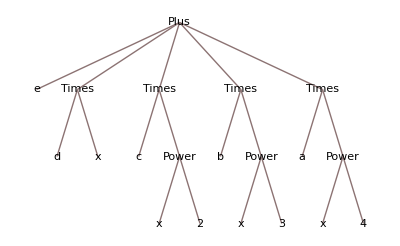

```mathematica
TreeForm[a x^4+b x^3+c x^2+d x+e] (*Power[x,n] только на 3-ем уровне*)
```

```mathematica
Cases[a x^4+b x^3+c x^2+d x+e,(var_)^n_,Infinity] (*искать везде!*)
```

{x^2,x^3,x^4}

#### Условные паттерны (Conditional pattern matching)

expr_ /; test 	- выражение, удовлетворяющее условию
expr_ ?test 	- сокращенная запись

```mathematica
Cases[{1,2,3,4,5,6,7,8,9},n_/;IntegerQ[√n]](*выбрать элементы, которые являются квадратами натуральных чисел*)
```

{1,4,9}

```mathematica
IntegerQ[√21]
```

False

```mathematica
Cases[{x,x^2,x^3,x^4,x^5},_^(n_)/;EvenQ[n]](*элементы в чётной степени*)
```

{x^2,x^4}

Является ли матрица квадратной ?

```mathematica
mat = RandomReal[1,{4,4}];
MatrixForm[mat]
```

(0.341893 | 0.576913 | 0.4374 | 0.640361
0.63936 | 0.0167767 | 0.914116 | 0.982088
0.831631 | 0.83793 | 0.901452 | 0.0500457
0.0193514 | 0.155429 | 0.151997 | 0.645362)

```mathematica
Dimensions[mat]
```

{4,4}

```mathematica
(*напишем функцию для проверки размерности матрицы*)
```

```mathematica
squareMatrixQ[mat_/;MatrixQ[mat]]:=Dimensions[mat]⟦1⟧ ==Dimensions[mat]⟦2⟧
```

```mathematica
squareMatrixQ[mat]
```

True

```mathematica
squareMatrixQ[RandomReal[1,{3,4}]]
```

False

```mathematica
squareMatrixQ[{{1}}] (*матрица 1х1*)
```

True

```mathematica
(*сокращенная запись*)
```

```mathematica
Cases[{1,2,3,4,5,6,7,8,9},_?PrimeQ]
```

{2,3,5,7}

```mathematica
MatchQ[-Graphics-,_?ImageQ]
```

True

```mathematica
MatchQ[{1,2,3},_List] (*проверяем "голову" выражения*)
```

True

```mathematica
MatchQ[{1,2,3},_?NumberQ] (*является ли, выражение числом*)
```

False

```mathematica
MatchQ[{1,2,3},{__?NumberQ}] (*является ли, выражение списком чисел*)
```

True

```mathematica
(*выбор по критерию*)
```

```mathematica
Cases[{1,2,3,a},_?NumberQ]
```

{1,2,3}

```mathematica
Cases[{-2,7,-1.2,0,-5-2 I},_?Negative]
```

{-2,-1.2}

```mathematica
Cases[Union[Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]],_?PrimeQ]
```

{2,3,5,7,17,31,127,257,8191,65537,131071,524287,2147483647}

```mathematica
Cases[Union[Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]],_?(#1<127&)]
```

{0,1,2,3,5,7,9,15,17,31,33,63,65}

Числа Фибоначчи

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_?IntegerQ]:=fib[n-1]+fib[n-2]
```

```mathematica
{fib[5],fib[10],fib[20],fib[1.2],fib[1+ⅈ]}
```

{5,55,6765,fib[1.2],fib[1+ⅈ]}

```mathematica
fib[-1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
(*ограничим аргумент только натуральными числами*)
```

```mathematica
Clear[fib]
```

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_/;IntegerQ[n]&&Positive[n]]:=fib[n-1]+fib[n-2]
```

```mathematica
{fib[5],fib[-10],fib[20],fib[1.2],fib[1+ⅈ]}
```

{5,fib[-10],6765,fib[1.2],fib[1+ⅈ]}

#### Альтернативы (Alternatives)

|p_1|p_2| ... |p_n - один из паттернов

```mathematica
Cases[{1,3.1,x,3+4 I,"Hello"},_Integer|_Rational|_Real]
```

{1,3.1}

```mathematica
Cases[{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0,0.0,"N/A"},Except[0,_?NumberQ]] (*все числа, кроме 0*)
```

{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0.}

```mathematica
Cases[{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0,0.0,"N/A"},Except[0|0.0,_?NumberQ]]
```

{-4.7943,-8.0251,7.2672,4.8205,-4.2002}

#### Functions that use patterns

```mathematica
ints=RandomInteger[20,{12}]
```

{20,16,16,11,17,18,6,20,5,6,16,11}

```mathematica
Cases[ints,x_/;Mod[x,3] ==0](*число, которые делятся на 3*)
```

{18,6,6}

```mathematica
Cases[ints,(x_/;Mod[x,3] ==2) | (x_/;Mod[x,3] ==1)]
```

{20,16,16,11,17,20,5,16,11}

```mathematica
DeleteCases[ints,(x_/;Mod[x,3] ==0) ]
```

{20,16,16,11,17,20,5,16,11}

```mathematica
Position[ints,x_/;Mod[x,3]== 0](*где в списке находятся элементы, удовлетворяющие условию*)
```

{{6},{7},{10}}

```mathematica
Count[ints,x_/;Mod[x,3]==0] (*сколько элементов списка, удовлетворяют условию*)
```

3

```mathematica
expr =∫Sqrt[x+Sqrt[x]]ⅆx
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
Depth[expr]
```

9

```mathematica
DeleteCases[expr,Sqrt[_],{4}]
```

1/12 √x (-1+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
DeleteCases[expr,Sqrt[_],4]
```

1/12 (-1+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
DeleteCases[expr,Sqrt[_],Infinity]
```

1/12 (-1+8 x)+Log[5]/8

Предварительная обработка данных

```mathematica
signal=Import["collectorData.dat","List"];
```

```mathematica
Take[signal,5062;;5080]
```

```mathematica
badvals=Count[signal,_String]
```

```mathematica
Count[signal,Except[_?NumericQ]]
```

```mathematica
Position[signal,_String]
```

1. Из списка натуральных чисел выбрать только те, которые делятся на 2 или 3 или 5.

2. Напишите функцию, которая работает только с натуральными числами и возвращает n/2, если n - четное число, и (3 n+1), если n - нечетное.

3. Напишите функцию, которая вычисляет модуль вещественных и комплексных чисел.

```mathematica
Cases[ints,(x_/;Mod[x,3] ==0) | (x_/;Mod[x,2] ==0)| (x_/;Mod[x,5] ==0)]
```

### Transformation rules

ReplaceAll[expr, pattern → replacement]

expr /. pattern → replacement - замена по правилу

```mathematica
x+y/.y->α
```

x+α

```mathematica
ReplaceAll[x+y,y->α]
```

x+α

```mathematica
{a,a}/.a->RandomReal[]
```

{0.241135,0.241135}

```mathematica
Trace[{a,a+a}/.a->RandomReal[]]
```

{{{a+a,2 a},{a,2 a}},{{RandomReal[],0.772726},a→0.772726,a→0.772726},{a,2 a}/.a→0.772726,{0.772726,2 0.772726},{2 0.772726,1.54545},{0.772726,1.54545}}

```mathematica
{a,a}/.a :>RandomReal[] (*Esc :> Esc отложенная замена*)
```

{0.0515279,0.838185}

```mathematica
Trace[{a,a}/.a :>RandomReal[] ]
```

{{a:>RandomReal[],a:>RandomReal[]},{a,a}/.a:>RandomReal[],{RandomReal[],RandomReal[]},{RandomReal[],0.918457},{RandomReal[],0.0339764},{0.918457,0.0339764}}

```mathematica
{a,b,c}/.List->Plus (*заменили "голову"*)
```

a+b+c

```mathematica
mat={{a,b,c},{d,e,f}};
```

```mathematica
MatrixForm[mat]
```

(a | b | c
d | e | f)

```mathematica
(*переставим столбцы*)
```

```mathematica
mat/.{col1_,col2_,col3_} :>{col1,col3,col2}//MatrixForm
```

(a | c | b
d | f | e)

```mathematica
(*заменим диагональные элементы*)
```

```mathematica
ReplacePart[mat,{i_,i_}->0]//MatrixForm
```

(0 | b | c
d | 0 | f)

```mathematica
{a,b,c}/.{c:> b,b:> a} (*правила применяются только один раз*)
```

{a,a,b}

```mathematica
{a,b,c}//.{c:> b,b:> a} (*правила применяются пока возможно*)
```

{a,a,a}

```mathematica
a b c d/.x_ y_ :>x+y
```

a+b c d

```mathematica
a b c d//.x_ y_:> x+y
```

a+b+c+d

```mathematica
{{x1,y1},{x2,y2},{x3,y3},x4,y4}/.{x_,y_} :>x+y (*вместо списка из 2х элементов - сумма элементов*)
```

{x1+y1,x2+y2,x3+y3,x4,y4}

```mathematica
(*отразим график относительно прямой y = x*)
```

```mathematica
gr=Plot[Sin[x],{x,0,2 π}];
```

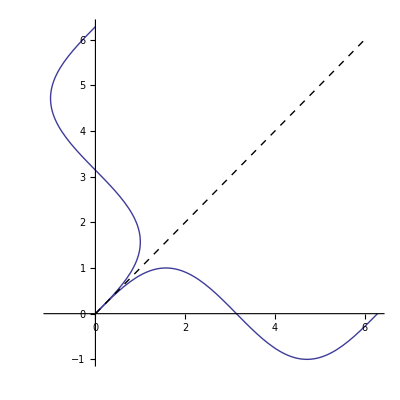

```mathematica
Show[{gr,gr/.{x_?NumberQ,y_?NumberQ} :>{y,x},Graphics[{Dashed,Line[{{0,0},{6,6}}]}]},PlotRange->All,AspectRatio->Automatic]
```

```mathematica
(*Замены можно делать, где угодно*)
```

```mathematica
StringReplace["acgttttccctgagcataaaaacccagcaatacg",{"ca"->"CA","tt"->"TT"}]
```

acgTTTTccctgagCAtaaaaaccCAgCAatacg

```mathematica
RandomReal[1,{3,3}]
```

{{0.289866,0.426779,0.582289},{0.211237,0.447899,0.485708},{0.207748,0.0381586,0.512884}}

```mathematica
{{0.2898,0.42677,"NAN"},{0.2112,0.4479,0.4857},{0.2077,"NAN",0.5129}}/.(_String->0.0)
```

{{0.2898,0.42677,0.},{0.2112,0.4479,0.4857},{0.2077,0.,0.5129}}

```mathematica
lis={f,12,"64",0.5,{a,b,c},-0.2,π};
```

```mathematica
Cases[lis,n_?NumericQ:> n^2]
```

{144,0.25,0.04,π^2}

4. С помощью паттернов получите только отрицательные вещественные корни следующего полинома
x^9 + 3.4 x^6 - 25 x^5 - 213 x^4 - 477 x^3 + 1012 x^2 + 111 x - 123

5. Напишите правило, которое делает список одномерным  (заменяет вложенные списки на последовательность из  элементов)

{{α, α, α}, {α}, {{β, γ, β}, {β, β}}, {α, α}} - >
{α, α, α, α, β, γ, β, β, β, α, α}

### Фильтрация данных

```mathematica
sig=Import["signal.dat","List"];
```

```mathematica
ListPlot[sig,PlotRange->{-1,1}]
```

ListPlot::lpn: sig is not a list of numbers or pairs of numbers.

ListPlot[sig,PlotRange→{-1,1}]

```mathematica
(* только данные из промежутка*)
```

```mathematica
filtered=Cases[sig,p_/;-0.3<p<0.3];
```

```mathematica
ListPlot[filtered,PlotRange->{-1,1}]
```

```mathematica
(**)
```

```mathematica
resData=Import["CAresevoir.csv","CSV"]
```

```mathematica
(*только те хранилища со средней емкостью < 75%, выводим только название и %*)
```

```mathematica
Cases[resData,{res_,__,avg_/;avg<75}:> {res,avg}]
```

### Сортировка списка

Создать правило, которое сортирует список чисел

```mathematica
nums=RandomReal[1,{10}]
```

{0.885754,0.976501,0.821957,0.278128,0.307913,0.979497,0.802003,0.994767,0.269543,0.259725}

```mathematica
listSort={{x___,a_?NumericQ,b_?NumericQ,y___} :>{x,b,a,y}/;b<a};
```

```mathematica
nums/.listSort
```

{0.885754,0.821957,0.976501,0.278128,0.307913,0.979497,0.802003,0.994767,0.269543,0.259725}

```mathematica
nums//.listSort
```

{0.259725,0.269543,0.278128,0.307913,0.802003,0.821957,0.885754,0.976501,0.979497,0.994767}

```mathematica
{ⅇ ,π,EulerGamma,GoldenRatio,1}//.listSort
```

{EulerGamma,1,GoldenRatio,ⅇ,π}

```mathematica
Sort[{ⅇ ,π,EulerGamma,GoldenRatio,1}]
```

{1,ⅇ,EulerGamma,GoldenRatio,π}

```mathematica
Sort[{ⅇ ,π,EulerGamma,GoldenRatio,1},Less]
```

{EulerGamma,1,GoldenRatio,ⅇ,π}